## Threshold expansion in Mellin Space

Before running this notebook, create a folder named datfiles in the same directory where this notebook is located.

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Physical constants

```mathematica
nc=3;nf=5;
CA=nc;CF=(nc^2-1)/(2nc);
β0=1/(12 π)(11 CA-2nf);(*A.1.3a*)
β1=(17 CA^2-(5CA+3CF)nf)/(24 π^2);(*A.1.3b*)
GF=1.166378 10^-5;
GevtoPb=3.8937966 10^8;
σ0[αs_]:=(αs^2 √2 GF)/(576π); (*C.1.3*)
A1g=CA/π;B1g=-β0;
A2g=CA/(2 π^2)(CA(67/18-Zeta[2])-5/9 nf);
A3g=CA/π^3((245/96-67/36 Zeta[2]+11/8 Zeta[4]+11/24 Zeta[3])CA^2+(5/18 Zeta[2]-209/432-7/12 Zeta[3])nf CA+(1/2 Zeta[3]-55/96)nf CF-1/108 nf^2);
β2=1/(4π)^3(2857/54 CA^3+(CF^2-205/18 CA CF-1415/54 CA^2)nf+(11/9 CF+77/54 CA)nf^2);
B2g=1/(16 π^2)(CA^2(-611/9+88/3 Zeta[2]+16 Zeta[3])+nf CA (428/27-16/3 Zeta[2])+2nf CF-20/27 nf^2);
```

#### LO coefficient (Mellin transform of the LO pt-distribution)

```mathematica
C0gg[αs_,n_]:=(2 αs CA)/π 1/ξp(Gamma[1/2]Gamma[n])/Gamma[n+1/2](Hypergeometric2F1[1/2,n,n+1/2,(√(1+ξp)-√ξp)^4]-2(1+ξp)/(√(1+ξp)+√ξp)^2 n/(n+1/2) Hypergeometric2F1[1/2,n+1,n+3/2,(√(1+ξp)-√ξp)^4] + ((1+ξp)(3+ξp))/(√(1+ξp)+√ξp)^4(n(n+1))/((n+1/2)(n+3/2))Hypergeometric2F1[1/2,n+2,n+5/2,(√(1+ξp)-√ξp)^4]-2(1+ξp)/(√(1+ξp)+√ξp)^6 (n(n+1)(n+2))/((n+1/2)(n+3/2)(n+5/2)) Hypergeometric2F1[1/2,n+3,n+7/2,(√(1+ξp)-√ξp)^4] + 1/(√(1+ξp)+√ξp)^8(n(n+1)(n+2)(n+3))/((n+1/2)(n+3/2)(n+5/2)(n+7/2))Hypergeometric2F1[1/2,n+4,n+9/2,(√(1+ξp)-√ξp)^4]);
```

#### Matching function

```mathematica
g01gg=67/36 CA - 5/18 nf + CA Zeta[2]-β0 Log[ξp/(1+ξp)]-1/8 CA Log[ξp/(1+ξp)]^2+2CA PolyLog[2,1-(√ξp)/(√(1+ξp))]+CA Log[1-(√ξp)/(√(1+ξp))]Log[ξp/(1+ξp)]-1/2 CA Log[1+(√ξp)/(√(1+ξp))]Log[ξp/(1+ξp)]+1/2 CA Log[1+(√ξp)/(√(1+ξp))]^2+2β0 Log[1+(√ξp)/(√(1+ξp))]^2+CA PolyLog[2,(2 √ξp)/(√(1+ξp)+√ξp)]-((CA-nf)(√ξp √(1+ξp)(1+ξp)-2ξp-ξp^2))/(6(1+8ξp+9 ξp^2)) ;
```

```mathematica
g0gg[αs_]:=1+(αs/π)g01gg;
```

#### Soft-large angle contributions

The correct expression of the soft large-angle contribution is given by:
S(Q^2)=ln(pt/Q)∫_0^1 ⅆz ((z^(N-1)-1)/(1-z)) A(α_s(Q^2(1-z)))  with Q=√(m_H^2+pt^2)+pt
To perform the above integration, we write
z^(N-1)-1=-Γ̃(1-∂/(∂ ln(N̄)))Θ(1-z-1/(N̄))+O(1/(N̄))  where up to NNLL Γ̃ can be written as  Γ̃(1-∂/(∂ ln(N̄)))=1+(ζ(2))/2(∂/(∂ ln(N̄)))^2
such that the above integral becomes
S(Q^2)=-ln(pt/Q)(1+(ζ(2))/2(∂/(∂ ln(N̄)))^2)∫_0^(1-1/N̄) ⅆz 1/(1-z) A(α_s(Q^2(1-z)))

```mathematica
(*Terms that contribute at NLL (and NNLL for the scale variation)*)
```

```mathematica
NLLA1=-Integrate[1/(1-z)αμ/(1+αμ β0 Log[(Q^2(1-z))/μr^2]),{z,0,1-1/Nbar},GenerateConditions->False]//Expand
```

-Log[1+αμ β0 Log[Q^2/μr^2]]/β0+Log[1+αμ β0 Log[Q^2/(Nbar μr^2)]]/β0

Now,  we can fix λ=αμ ln(N̄) and expand the rest as a series in αμ.

```mathematica
NLLA1/.{Log[Q^2/(Nbar μr^2)]-> -LN+Log[Q^2/μr^2]}/.{αμ β0 LN-> λ}
```

-Log[1+αμ β0 Log[Q^2/μr^2]]/β0+Log[1+αμ β0 (-LN+Log[Q^2/μr^2])]/β0

```mathematica
Collect[Normal@Series[-Log[1+αμ β0 Log[Q^2/μr^2]]/β0+Log[1-λ+αμ β0 Log[Q^2/μr^2]]/β0/.{Log[Q^2/μr^2]-> LQR},{αμ,0,2}],αμ](*LQR=LR+2*Log[√(1+ξp)+√ξp]*)
```

αμ^2 ((LQR^2 β0)/2-(LQR^2 β0)/(2 (-1+λ)^2))-(LQR αμ λ)/(-1+λ)+Log[1-λ]/β0

At NLL, only the term that is not multiplied by αμ contribute, while the terms that are multiplied by αμ and αμ^2 contribute at NNLL and NNNLL respectively.

```mathematica
(*Terms that contribute at NNLL*)
```

```mathematica
NNLLA2=Together[-Integrate[1/(1-z)(αμ/(1+αμ β0 Log[(Q^2(1-z))/μr^2]))^2,{z,0,1-1/Nbar},GenerateConditions->False]]
```

-(αμ^2 (Log[Q^2/μr^2]-Log[Q^2/(Nbar μr^2)]))/((1+αμ β0 Log[Q^2/μr^2]) (1+αμ β0 Log[Q^2/(Nbar μr^2)]))

```mathematica
Collect[Series[-(αμ λ)/(β0(1+αμ β0 Log[Q^2/μr^2]) (1-λ+αμ β0 Log[Q^2/μr^2]))/.{Log[Q^2/μr^2]-> LQR},{αμ,0,2}],αμ]
```

-(LQR αμ^2 (-2+λ) λ)/(-1+λ)^2+(αμ λ)/(β0 (-1+λ))

```mathematica
NNLLA1=β1/β0 Integrate[1/(1-z)αμ^2/((1+αμ β0 Log[(Q^2(1-z))/μr^2])^2)Log[1+αμ β0 Log[(Q^2(1-z))/μr^2]],{z,0,1-1/Nbar},GenerateConditions->False]
```

(αμ β1 (-(1+Log[1+αμ β0 Log[Q^2/μr^2]])/(1+αμ β0 Log[Q^2/μr^2])+(1+Log[1+αμ β0 Log[Q^2/(Nbar μr^2)]])/(1+αμ β0 Log[Q^2/(Nbar μr^2)])))/β0^2

```mathematica
Collect[Series[αμ β1/β0^2 (-(1+Log[1+αμ β0 Log[Q^2/μr^2]])/(1+αμ β0 Log[Q^2/μr^2])+(1+Log[1-λ+αμ β0 Log[Q^2/μr^2]])/(1-λ+αμ β0 Log[Q^2/μr^2]))/.{Log[Q^2/μr^2]-> LQR},{αμ,0,2}],αμ]
```

-(LQR αμ^2 β1 Log[1-λ])/(β0 (-1+λ)^2)-(αμ β1 (λ+Log[1-λ]))/(β0^2 (-1+λ))

Both in NNLLA1 and NNLLA2, the terms multiplied by αμ contribute at NNLL, while the terms that are proportional to αμ^2 (that takes into account the variation of scales) contribute at NNNLL.

#### Corrected resummed exponents

```mathematica
(* In oder to get the pt-dependent part in the following expressions, we perform the following replaacement: λ-> λnbar/2 [see below for the definition of λnbar] *)
```

```mathematica
g1gg[αs_]:=(Agth1/β0^2)(λnbar+((1-λnbar)/2)Log[1-λnbar]+(1-λnbar/2)Log[1-λnbar/2])(*/.{λnbar-> αs β0 Log[nbar^2]}/.{nbar-> n Exp[EulerGamma]}*);
g2gg[αs_]:=-((Agth1 β1)/β0^3)(λnbar+(1/2)Log[1-λnbar]+(1/4)Log[1-λnbar]^2+Log[1-λnbar/2]+(1/2)Log[1-λnbar/2]^2)-(Agth2/β0^2)((1/2)Log[1-λnbar]+λnbar+Log[1-λnbar/2])+(Bgth1/β0)Log[1-λnbar/2]+(Agth1/β0)Log[1-λnbar/2]Log[(√ξp)/(√(1+ξp)+√ξp)]+(Agth1/β0)((1/2)Log[1-λnbar]+λnbar+Log[1-λnbar/2])LR-2 (Agth1/β0)λnbar LF;
g3gg[αs_]:=(Agth1/(4 β0^4(1-λnbar)(2-λnbar)))(λnbar^2(3-2λnbar)+2(2-λnbar)λnbar(1-λnbar)+(2-λnbar)Log[1-λnbar]^2+4(1-λnbar)λnbar Log[1-λnbar/2]+4(1-λnbar)Log[1-λnbar/2]^2)+((Agth1 β2)/(4 β0^3))((λnbar(8-9λnbar+2 λnbar^2))/((2-λnbar)(1-λnbar))+2 Log[1-λnbar]+4Log[1-λnbar/2])+((Agth2 β1)/(4 β0^3(1-λnbar)(2-λnbar)))(λnbar(2 λnbar^2+3λnbar-8)-2(2-λnbar)Log[1-λnbar]-8(1-λnbar)Log[1-λnbar/2])+(Agth3/(4 β0^2))(((3-2λnbar)λnbar^2)/((1-λnbar)(2-λnbar)))-((Bgth1 β1)/β0^2)((λnbar+2Log[1-λnbar/2])/(2-λnbar))-(Bgth2 /β0)(λnbar/(2-λnbar))+((Agth1 β1)/β0^2)((λnbar/2+Log[1-λnbar/2])/(1-λnbar/2))Log[(√ξp)/(√(1+ξp)+√ξp)]-(Agth2/β0)(λnbar/2/(1-λnbar/2))Log[(√ξp)/(√(1+ξp)+√ξp)]-Agth1 Zeta[2] ((3-2λnbar)/((1-λnbar)(2-λnbar)))+(Agth1/4)(((3-2λnbar)λnbar^2)/((1-λnbar)(2-λnbar)))LR^2-Agth1 λnbar LR^2+(Agth1/(2β0))(β1/((1-λnbar)(2-λnbar)))((4-3λnbar)λnbar+(2-λnbar)Log[1-λnbar]+4(1-λnbar)Log[1-λnbar/2])LR+2Agth1 λnbar LR LF-(Agth2/(2 β0))(((3-2λnbar)λnbar^2)/((1-λnbar)(2-λnbar)))LR+2(Agth2/ β0) λnbar LF+Bgth1 (λnbar/(2-λnbar))LR+Agth1 (λnbar/2/(1-λnbar/2))(LR +2Log[√(1+ξp)+√ξp])(*double check this last term*);
```

Full resummed results

#### Generating data for plotting

```mathematica
αss=0.108316;nn=3;pt=10;Q=125;mH=125;μR=165;μF=165;
dσResgg[αs_,n_,pt_,mH_]:=C0gg[αs,n]g0gg[αs]Exp[1/αs g1gg[αs]+g2gg[αs]+αs g3gg[αs]]/.{ξp-> pt^2/mH^2}/.{λnbar-> αs β0 Log[nbar^2]}/.{nbar-> n Exp[EulerGamma]};
dσResggNLL[αs_,n_,pt_]:=(2 pt)/mH^2 (GevtoPb)σ0[αs]dσResgg[αs,n,pt,mH]/.{Agth1-> A1g,Agth2-> A2g,Agth3-> A3g,Bgth1-> B1g,Bgth2-> B2g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2],LRF-> 0};
```

```mathematica
resNNLLggasN=Table[{n,1/(σ0[αss] GevtoPb)dσResggNLL[αss,n,pt]},{n,1,20}];
Export["./datfiles/resNNLLggasN.dat",resNNLLggasN,"Table"];
```

```mathematica
resNNLLggaspt=Table[{pt,1/(σ0[αss] GevtoPb)dσResggNLL[αss,nn,pt]},{pt,1,40}];
Export["./datfiles/resNNLLggaspt.dat",resNNLLggaspt,"Table"];
```

Series expansion in αs

#### Expansion of the resummed expression

```mathematica
dσgg[αs_,n_,pt_,mH_,res_]:=C0gg[αs,n](*(1+αs G01GG)*)g0gg[αs]Exp[1/αs g1gg[αs]+Which[res==1,0,res==2,g2gg[αs],res==3,g2gg[αs]+αs g3gg[αs]]]/.{ξp-> pt^2/mH^2}/.{λnbar-> αs β0 Log[nbar^2]}/.{nbar-> n Exp[EulerGamma]};
```

```mathematica
Expdσgg[order_,αs_,n_,pt_,mH_,res_]:=Normal@Series[dσgg[α,n,pt,mH,res],{α,0,order}]/.{α-> αs};
```

Up to αs-terms (basically the LO pt-distribution or C0)

#### Numerical checks

```mathematica
αss=0.11264;nn=3;pt=10;Q=125;mH=125;μR=125;μF=125;(*mH=μR=μF*)
```

```mathematica
ExpdσggLO[αs_,n_,pt_]:=(2 pt)/mH^2 (GevtoPb)σ0[αs]Expdσgg[1,αs,n,pt,mH,2]/.{Agth1-> A1g,Agth2-> A2g,Bgth1-> B1g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2]};
```

```mathematica
{Map[ExpdσggLO[αss,nn,#]&,{10,20,30}],Map[ExpdσggLO[αss,20,#]&,{10,20,30}]}//N
```

{{0.00237928,0.000852695,0.000479992},{0.00106449,0.000349261,0.000186276}}

#### Generating data for plotting

```mathematica
C0expLOaspt=Table[{pt,ExpdσggLO[αss,nn,pt]},{pt,1,150}];
Export["./datfiles/C0expLOaspt.dat",C0expLOaspt,"Table"];
```

```mathematica
C0expLOasN=Table[{n,ExpdσggLO[αss,n,10]},{n,1,20}];
Export["./datfiles/C0expLOasN.dat",C0expLOasN,"Table"];
```

#### Plots

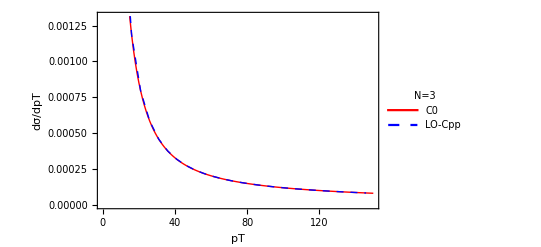

```mathematica
ListLinePlot[{Import["./datfiles/C0expLOaspt.dat","Table"],Import["./datfiles/higgspts_as_pt_N3_LO_gg_channel.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},PlotLegends->Placed[LineLegend[{"C0","LO-Cpp"},LabelStyle->{Black,10},LegendLabel->"N=3",LegendFunction->"Frame"],{0.7,0.5}],FrameLabel->{{"dσ/dpT",""},{"pT", "C0 coeffs."}}]
```

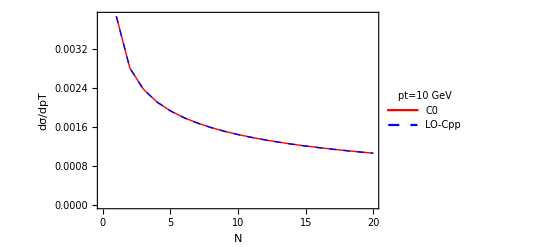

```mathematica
ListLinePlot[{Import["./datfiles/C0expLOasN.dat","Table"],Import["./datfiles/higgs_as_N_pt10GeV_LO_gg_channel.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},PlotLegends->Placed[LineLegend[{"C0","LO-Cpp"},LabelStyle->{Black,10},LegendLabel->"pt=10 GeV",LegendFunction->"Frame"],{0.64,0.65}],FrameLabel->{{"dσ/dpT",""},{"N", "C0 coeffs."}}]
```

Up to αs^2-terms

#### Numerical checks

```mathematica
αss=0.11264;nn=3;pt=10;Q=125;mH=125;μR=125;μF=125;NN=20;
```

```mathematica
ExpdσggNLO[αs_,n_,pt_,res_]:=(2 pt)/mH^2 (GevtoPb)σ0[αs]Expdσgg[2,αs,n,pt,mH,res]/.{Agth1-> A1g,Agth2-> A2g,Bgth1-> B1g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2]};
```

```mathematica
ptval=Table[pt,{pt,10,200,10}];
```

```mathematica
{Map[ExpdσggNLO[αss,nn,#,1]&,{10,20,30}],Map[ExpdσggNLO[αss,NN,#,1]&,{10,20,30}]}//N
```

{{0.00457349,0.00175695,0.00101483},{0.00375638,0.00128076,0.000693107}}

```mathematica
{Map[ExpdσggNLO[αss,nn,#,2]&,{10,20,30}],Map[ExpdσggNLO[αss,NN,#,2]&,{10,20,30}]}//N
```

{{0.00596501,0.00216132,0.00121416},{0.00508372,0.00163389,0.000858031}}

```mathematica
{Map[ExpdσggNLO[αss,nn,#,3]&,{10,20,30}],Map[ExpdσggNLO[αss,NN,#,3]&,{10,20,30}]}//N
```

{{0.00533355,0.00193501,0.00108677},{0.00480121,0.00154119,0.000808593}}

#### Generating data for plotting

```mathematica
(*Expansion of the LL resummed expression to LO*)
```

```mathematica
LLexpNLOasN=Table[{n,ExpdσggNLO[αss,n,pt,1]},{n,1,1500,5}];
Export["./datfiles/LLexpNLOasN.dat",LLexpNLOasN,"Table"];
```

```mathematica
LLexpNLOasPt=Table[{pt,ExpdσggNLO[αss,nn,pt,1]},{pt,1,150}];(*Large N*)
Export["./datfiles/LLexpNLOasPt.dat",LLexpNLOasPt,"Table"];
```

```mathematica
(*Expansion of the NLL resummed expression to NLO*)
```

```mathematica
NLLexpNLOasN=Table[{n,ExpdσggNLO[αss,n,pt,2]},{n,1,1500,5}];
Export["./datfiles/NLLexpNLOasN.dat",NLLexpNLOasN,"Table"];
```

```mathematica
NLLexpNLOasPt=Table[{pt,ExpdσggNLO[αss,nn,pt,2]},{pt,1,150}];(*Large N*)
Export["./datfiles/NLLexpNLOasPt.dat",NLLexpNLOasPt,"Table"];
```

```mathematica
(*Expansion of the NNLL resummed expression to NLO*)
```

```mathematica
NNLLexpNLOasN=Table[{n,ExpdσggNLO[αss,n,pt,3]},{n,1,1500,5}]//N;
Export["./datfiles/NNLLexpNLOasN.dat",NNLLexpNLOasN,"Table"];
```

```mathematica
NNLLexpNLOasPt=Table[{pt,ExpdσggNLO[αss,nn,pt,3]},{pt,1,150}];(*Large N*)
Export["./datfiles/NNLLexpNLOasPt.dat",NNLLexpNLOasPt,"Table"];
```

#### Plots

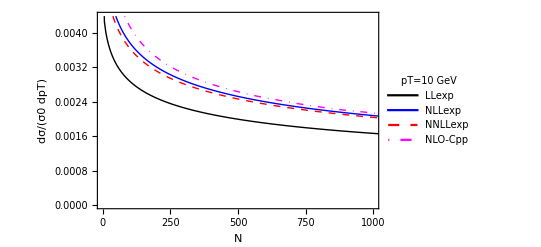

```mathematica
ListLinePlot[{Import["./datfiles/LLexpNLOasN.dat","Table"],Import["./datfiles/NLLexpNLOasN.dat","Table"],Import["./datfiles/NNLLexpNLOasN.dat"],Import["./datfiles/higgs_as_N_pt10GeV_NLO_gg_channel.dat"]},Frame->True,FrameStyle->Directive[Black,12],
PlotStyle->{{Thick,Black},{Thick,Blue},{Dashed,Thick,Red},{DotDashed,Thick,Magenta}},PlotLegends->Placed[LineLegend[{"LLexp","NLLexp","NNLLexp","NLO-Cpp"},LabelStyle->{Black,10},LegendLabel->"pT=10 GeV",LegendFunction->"Frame",LegendLayout->{"Column",2}],{0.5,0.175}],
FrameLabel->{{"dσ/(σ0 dpT)",""},{"N", "NLL/NNLL threshold expanded to NLO"}}, PlotRange->{{0,1000},Automatic}]
(*also normalized with GevtoPb*)
```

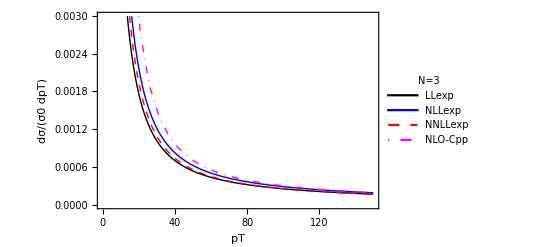

```mathematica
ListLinePlot[{Import["./datfiles/LLexpNLOasPt.dat"],Import["./datfiles/NLLexpNLOasPt.dat"],Import["./datfiles/NNLLexpNLOasPt.dat"],Import["./datfiles/higgspts_as_pt_N3_NLO_gg_channel.dat"]},Frame->True,FrameStyle->Directive[Black,12],
PlotStyle->{{Thick,Black},{Thick,Blue},{Dashed,Thick,Red},{DotDashed,Thick,Magenta}},PlotLegends->Placed[LineLegend[{"LLexp","NLLexp","NNLLexp","NLO-Cpp"},LabelStyle->{Black,10},LegendLabel->"N=3",LegendFunction->"Frame"],
{0.7,0.5}],FrameLabel->{{"dσ/(σ0 dpT)",""},{"pT", "NLL/NNLL threshold expanded to NLO"}}]
(*also normalized with GevtoPb*)
```

Resummed expansion

#### NLO term only (proportional to αs^2):

```mathematica
Clear[nf,CA,CF,β0,β1,β2,GF,σ0,pt,mH];
```

```mathematica
dAΣgg[αs_,res_]:=dLOdpt Exp[1/αs g1gg[αs]+Which[res==1,0,res==2,g2gg[αs],res==3,g2gg[αs]+αs g3gg[αs]]];(*dLOpt contains an αs-dependence*)
```

```mathematica
ExpdAΣgg[order_,αs_,n_,res_]:=Normal@Series[dAΣgg[α,res]/.{λnbar-> α β0 LNb2},{α,0,order}]/.{α-> αs};
```

```mathematica
Collect[Coefficient[ExpdAΣgg[1,αs,n,3]//Expand,αs,1],{dLOdpt,LNb2}]
```

dLOdpt ((3 Agth1 LNb2^2)/8-(Agth1 π^2)/4+LNb2 (-Bgth1/2-2 Agth1 LF-1/2 Agth1 Log[(√ξp)/(√ξp+√(1+ξp))]))

#### Generate data for plotting:

```mathematica
αss=0.11264;nn=3;pt=10;Q=125;mH=125;μR=125;μF=125;NN=20;
```

```mathematica
ExpdNΣggNLO[αs_,n_,pt_]:=αs (2 pt)/mH^2 (GevtoPb)σ0[αs]dLOdpt ((3 Agth1 LNb2^2)/8-(3Agth1)/2 Zeta[2]+LNb2 (-Bgth1/2-2 Agth1 LF-1/2 Agth1 Log[(√ξp)/(√ξp+√(1+ξp))]))/.{dLOdpt-> C0gg[αs,n]}/.{ξp-> pt^2/mH^2}/.{LNb2-> Log[nbar^2]}/.{nbar-> n Exp[EulerGamma]}/.{Agth1-> A1g,Agth2-> A2g,Bgth1-> B1g}/.{LR-> Log[mH^2/μR^2],LF-> Log[mH^2/μF^2],LQ-> Log[mH^2/Q^2]};
```

```mathematica
NLOTermasN=Table[{n,ExpdNΣggNLO[αss,n,pt]},{n,1,1500,5}];
Export["./datfiles/NLOTermasN.dat",NLOTermasN,"Table"];
```

#### Plots:

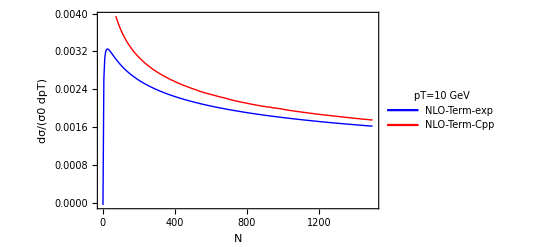

```mathematica
ListLinePlot[{Import["./datfiles/NLOTermasN.dat","Table"],Import["./datfiles/NLOTerm_as_N_pt10GeV_NLO_gg_channel.dat","Table"]},Frame->True,FrameStyle->Directive[Black,12],PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->Placed[LineLegend[{"NLO-Term-exp","NLO-Term-Cpp"},
LabelStyle->{Black,10},LegendLabel->"pT=10 GeV",LegendFunction->"Frame"],{0.5,0.175}],FrameLabel->{{"dσ/(σ0 dpT)",""},{"N", "NLL/NNLL threshold NLO term"}}, PlotRange->{{0,1500},Automatic}]
```

Analytical limits

```mathematica
(*The small-pT limit of the LO has been derived in other notebooks and shown to be the same as in the expansion of the Small-pT limit*)
```

```mathematica
Clear[nf,CA,CF,β0,β1,β2,GF,σ0,pt,mH];
```

```mathematica
dΣgg[αs_,res_]:=αs C0GG(1+αs G01GG)Exp[1/αs g1gg[αs]+Which[res==1,0,res==2,g2gg[αs],res==3,g2gg[αs]+αs g3gg[αs]]];
```

```mathematica
ExpdΣgg[order_,αs_,n_,pt_,res_]:=Normal@Series[dΣgg[α,res]/.{C0GG-> 1/α C0gg[α,n],G01GG->g01gg }/.{λnbar-> α β0 Log[nbar^2]}/.{nbar-> n Exp[EulerGamma]},{α,0,order}]/.{α-> αs};
```

#### Expansion up to αs:

```mathematica
COsmallpt=Assuming[ξp≥0&&√ξp n>1,Normal@Series[ExpdΣgg[1,αs,n,ξp,3],{ξp,0,-1}]//FunctionExpand];
```

```mathematica
COsmallptLargeN=Collect[Normal@Series[COsmallpt,{n,Infinity,0}],{Ca,Log[_]},Factor]
```

-(2 CA EulerGamma αs)/(π ξp)-(2 CA αs Log[n])/(π ξp)-(CA αs Log[ξp])/(π ξp)

#### Expansion up to αs^2:

```mathematica
COsmallptNLO=Assuming[ξp≥0&&√ξp n>1,Normal@Series[ExpdΣgg[2,αs,n,ξp,3],{ξp,0,-1}]//FunctionExpand];
```

$Aborted

```mathematica
COsmallptNLOLargeN=Collect[Normal@Series[COsmallptNLO,{n,Infinity,0}],{Ca,Log[_]},Factor];
```

```mathematica
Collect[COsmallptNLOLargeN/.{Log[ξp]-> LpT,ξp-> pT^2/MH^2,Log[n]-> LN+EulerGamma}//Expand//FullSimplify,{αsp,LpT}]
```

(3 CA LpT^3 MH^2 αs^2)/(8 π pT^2)-(CA LpT^2 MH^2 αs (-138 αs-108 EulerGamma π αs-54 LN π αs-36 Agth1 (2 EulerGamma+LN) π αs))/(72 π^2 pT^2)-1/(72 π^2 pT^2)CA LpT MH^2 αs (72 π-552 EulerGamma αs-276 LN αs+302 π αs-72 Bgth1 (2 EulerGamma+LN) π αs+72 Agth1 EulerGamma (2 EulerGamma+LN) π αs-288 Agth1 LF (2 EulerGamma+LN) π αs+36 Agth1 LN (2 EulerGamma+LN) π αs-18 (-6+Agth1) π^3 αs)-1/(72 π^2 pT^2)CA MH^2 αs (288 EulerGamma π+144 LN π+1208 EulerGamma π αs+604 LN π αs-288 Bgth1 EulerGamma (2 EulerGamma+LN) π αs+864 Agth1 EulerGamma^2 (2 EulerGamma+LN) π αs-1152 Agth1 EulerGamma LF (2 EulerGamma+LN) π αs-144 Bgth1 LN (2 EulerGamma+LN) π αs+864 Agth1 EulerGamma LN (2 EulerGamma+LN) π αs-576 Agth1 LF LN (2 EulerGamma+LN) π αs+216 Agth1 LN^2 (2 EulerGamma+LN) π αs-72 (-6+Agth1) EulerGamma π^3 αs-36 (-6+Agth1) LN π^3 αs)

Appendix